# Project Coding Template APPM 2350 : Spring 2018 Authors: Mattias Leino Derek Thomas

```mathematica
Clear["Global`*"]
```

## Section 3: Observers at three different latitudes

```mathematica
(* Functions *)
Θ[t_] := -0.41 * Cos[(2π*t)/ 365.25]
x[t_,ϕ_] := Cos[ϕ] * Sin[2π*t]
y[t_,ϕ_] := -Cos[ϕ] * Cos[2π*t] * Cos[Θ[t]] + Sin[ϕ] * Sin[Θ[t]]
z[t_, ϕ_] := Cos[ϕ] * Cos[2π * t] * Sin[Θ[t]] + Sin[ϕ] * Cos[Θ[t]]
n[t_,ϕ_] := Cos[ϕ] * Sin[Θ[t]] + Sin[ϕ] * Cos[Θ[t]] * Cos[2 * π * t]
e[t_, ϕ_] := Cos[Θ[t]] * Sin[2 * π * t]
u[t_, ϕ_] := (1 - n[t,ϕ]^2 - e[t,ϕ]^2)^(1/2)
η[t_, ϕ_] := ArcSin[u[t,ϕ]]
```

```mathematica
(* Latitudes of the locations we are looking at *)
boulderLat = 0.6981;
chichenitzaLat = 0.3613;
southpoleLat = 1.5708;
```

This is a plot of the position of the sun above and below the horizon (y=0) over the course of 5 days.

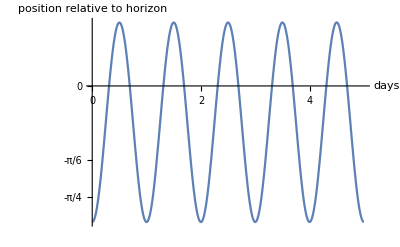

```mathematica
Plot[{y[t,0.698132]},{t,0,5}, AxesLabel->{"days","position relative to horizon"}, Ticks->{{0,1,2,3,4,5},{-π/4, -π/6,0,π/6,π/4}}]
```

```mathematica
(* Using the FindRoot fucntion to build a table of all the times the y(t,ϕ) function finds zero. i.e. When the sun crosses the horizon, either sunrise or sunset *)
days ={t} /. Table[FindRoot[y[t,boulderLat]==0, {t, day -0.25}], {day, 0.5, 365,0.5}] ;

(*creates a list of day lengths *)
riseIndex = 1;
setIndex = 2;
rise = 0;
set = 0;
dayLengths = {};
(*Loop iterates through each sunrise and sunset and finds the difference
then stores these differences in a list called day lengths*)
While[riseIndex < 730, 
rise = Part[days,riseIndex]; 
set = Part[days, setIndex]; 
AppendTo[dayLengths,(set-rise)];
 riseIndex = riseIndex+2; setIndex = setIndex+2];

(*some tests + printing min and max*)
Print["Stats for Boulder"]
Print["Length of longest day"]
Max[dayLengths]
Print["Index of longest day"]
Position[dayLengths,Max[dayLengths]]
Print["Length of shortest day"]
Min[dayLengths]
Print["Index of shortest day"]
Position[dayLengths,Min[dayLengths]]

(*Find equinox function takes a range of days and finds the day in the range that is the closest
to exactly half day.  Then it stores the index (day number) and the length of the day found*)

findEquinox[loopStart_,loopEnd_] :=(
candidate = 0;
currentMin =1;
indexOfEquinox = -1;
For[i=loopStart,i<loopEnd,i++,
candidate = Part[Part[dayLengths,i],1];
currentDist = Abs[.5-currentMin];
candidateDist = Abs[.5-candidate];
currentMin = If[candidateDist < currentDist, candidate, currentMin];
indexOfEquinox = If[candidateDist < currentDist, i, indexOfEquinox];
]
)

(*Because there are two equinoxes find equinox needs to be called twice, once on each half of the year*)
findEquinox[1,181];
Print["First equinox:"]
Print["Length of day:"]
currentMin
Print["Day number:"]
indexOfEquinox

findEquinox[181,361];
Print["Second equinox:"]
Print["Length of day"]
currentMin
Print["Day number:"]
indexOfEquinox
```

Stats for Boulder

Length of longest day

0.618818

Index of longest day

{{183,1}}

Length of shortest day

0.381186

Index of shortest day

{{1,1}}

First equinox:

Length of day:

0.500354

Day number:

92

Second equinox:

Length of day

0.500825

Day number:

274

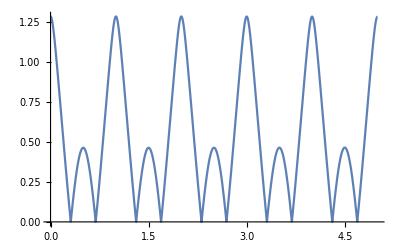

```mathematica
Plot[{η[t,0.698132]},{t,0,5}]
```

```mathematica
(* *)
RiseAngle[dayRA_,phiRA_] := 
(srtRA = FindRoot[y[tRA, phiRA] == 0, {tRA, Round[dayRA] -0.75}];
180*ArcCos[n[tRA/.srtRA,phiRA]]/Pi);
```

```mathematica
boulderRA = Table[RiseAngle[dayRA,40*Pi/180],{dayRA,0,365,1}];
```

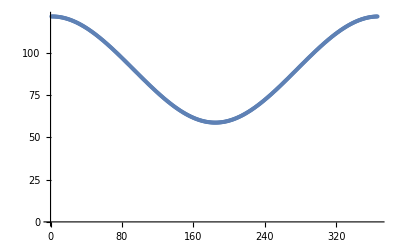

```mathematica
ListPlot[boulderRA]
```

```mathematica
mexicoDays ={t} /. Table[FindRoot[y[t,chichenitzaLat]==0, {t, day -0.25}], {day, 0.5, 365,0.5}] ;


(*creates a list of day lengths *)
riseIndex = 1;
setIndex = 2;
rise = 0;
set = 0;
dayLengths = {};(*Clears old list*)
While[riseIndex < 730, 
rise = Part[mexicoDays,riseIndex]; 
set = Part[mexicoDays, setIndex]; 
AppendTo[dayLengths,(set-rise)];
 riseIndex = riseIndex+2; setIndex = setIndex+2];

(*some tests + printing min and max*)
Print["Stats for Chichen Itza"]
Print["Length of longest day"]
Max[dayLengths]
Print["Index of longest day"]
Position[dayLengths,Max[dayLengths]]
Print["Length of shortest day"]
Min[dayLengths]
Print["Index of shortest day"]
Position[dayLengths,Min[dayLengths]]

(*Find equinoxes for Chichen Itza*)
findEquinox[1,181];
Print["First equinox:"]
Print["Length of day:"]
currentMin
Print["Day number:"]
indexOfEquinox

findEquinox[181,361];
Print["Second equinox:"]
Print["Length of day"]
currentMin
Print["Day number:"]
indexOfEquinox
```

Stats for Chichen Itza

Length of longest day

0.552517

Index of longest day

{{183,1}}

Length of shortest day

0.447485

Index of shortest day

{{1,1}}

First equinox:

Length of day:

0.500159

Day number:

92

Second equinox:

Length of day

0.500371

Day number:

274

```mathematica
southPoleDays ={t} /. Table[FindRoot[y[t,southpoleLat]==0, {t, day -0.25}], {day, 0.5, 365,0.5}] ;

(*creates a list of day lengths *)
riseIndex = 1;
setIndex = 2;
rise = 0;
set = 0;
dayLengths = {};
While[riseIndex < 730, 
rise = Part[southPoleDays,riseIndex]; 
set = Part[southPoleDays, setIndex]; 
AppendTo[dayLengths,(set-rise)];
 riseIndex = riseIndex+2; setIndex = setIndex+2];

(*some tests + printing min and max*)
Print["Stats for South Pole"]
Print["Length of longest day"]
Max[dayLengths]
Print["Index of longest day"]
Position[dayLengths,Max[dayLengths]]
Print["Length of shortest day"]
Min[dayLengths]
Print["Index of shortest day"]
Position[dayLengths,Min[dayLengths]]

(*Equinoxes for South Pole*)
findEquinox[1,181];
Print["First equinox:"]
Print["Length of day:"]
currentMin
Print["Day number:"]
indexOfEquinox

findEquinox[181,361];
Print["Second equinox:"]
Print["Length of day"]
currentMin
Print["Day number:"]
indexOfEquinox
```

Stats for South Pole

Length of longest day

730.5

Index of longest day

{{186,1}}

Length of shortest day

-3469.87

Index of shortest day

{{182,1}}

First equinox:

Length of day:

1.13687×10^-13

Day number:

177

Second equinox:

Length of day

1.36424×10^-12

Day number:

185

## Section 4: Radiant flux and the seasons

```mathematica
(* Calculating absolute error introduced by treating sun as a point source *)
```

```mathematica
sunDiameter = 2*7.0*10^5;
earthToSun = 1.5 * 10^8;

(* calculating maximum relative error of earth sun distance introduced by treating earth's orbit as circular *)

(* using values from tables create a table of *)
r[t_,ϕ_] := {x[t,ϕ],y[t,ϕ],z[t,ϕ]};
FluxInside[t_,ϕ_] := Dot[{0,1,0},r[t,ϕ]];

NIntegrate[FluxInside[t,boulderLat],{t,1,2}]
```

-0.256129

# Appendix

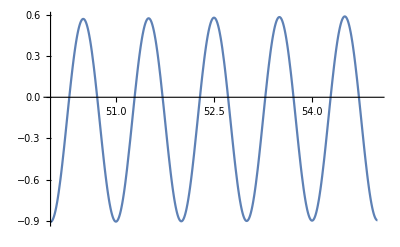

```mathematica
Plot[{y[t,0.698132]},{t,50,55}]
```

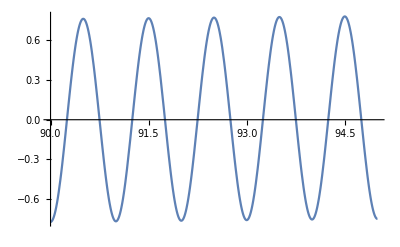

```mathematica
Plot[{y[t,0.698132]},{t,90,95}]
```

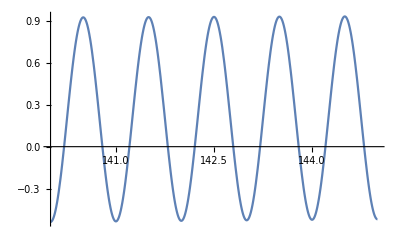

```mathematica
Plot[{y[t,0.698132]},{t,140,145}]
```

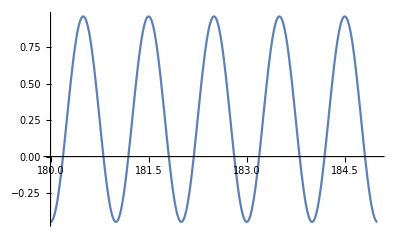

```mathematica
Plot[{y[t,0.698132]},{t,180,185}]
```

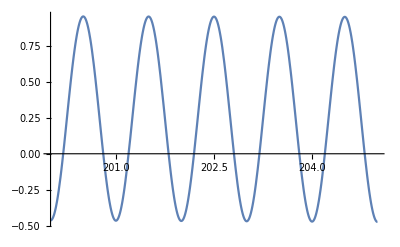

```mathematica
Plot[{y[t,0.698132]},{t,200,205}]
```

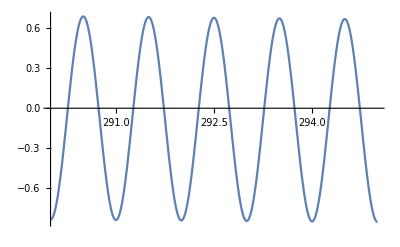

```mathematica
Plot[{y[t,0.698132]},{t,290,295}]
```

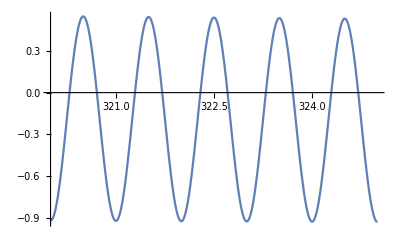

```mathematica
Plot[{y[t,0.698132]},{t,320,325}]
```